#### Step H: Histogram plots

```mathematica
filenameVolumeBase="FR96D1_";
pathVolumesFitted="/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/"
concFR=Import[pathVolumesFitted<>filenameVolumeBase<>"latest_vol_percent_MF1_FR.h5",{"Datasets","concFR"}];
Dimensions[concFR]
```

/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/

{256,651,623}

```mathematica
100*Max[concFR]
```

10.735

```mathematica
SeedRandom[1];
listOfNonZeroVoxels = Select[Flatten[concFR],#>0&];//Timing
Length[listOfNonZeroVoxels]
```

{166.931,Null}

44925700

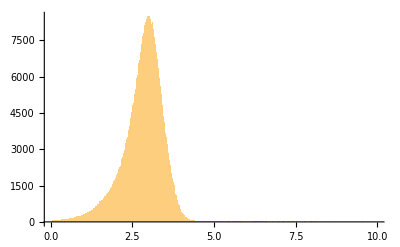

2.81817

0.601959

```mathematica
Histogram[RandomSample[100*listOfNonZeroVoxels,1000000],{0.0,10,0.01}]
100*Mean[listOfNonZeroVoxels]
100*StandardDeviation[listOfNonZeroVoxels]
```

```mathematica
(*______________________________________*)
```

```mathematica
filenameVolumeBase="FR96D1_";
pathVolumesFitted="/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/"
concSb2O3=Import[pathVolumesFitted<>filenameVolumeBase<>"latest_vol_percent_MF1_Sb2O3.h5",{"Datasets","concSb2O3"}];
```

/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/

```mathematica
Dimensions[concSb2O3]
100*Max[concSb2O3]

SeedRandom[1];
listOfNonZeroVoxels = Select[Flatten[concSb2O3],#>0&];//Timing
Length[listOfNonZeroVoxels]
```

{256,651,623}

14.9237

{167.59,Null}

44139919

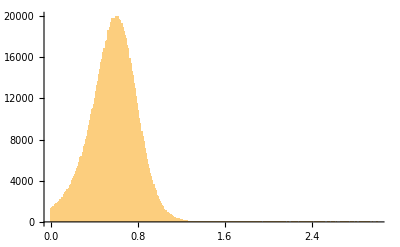

0.5772

0.217449

```mathematica
Histogram[RandomSample[100*listOfNonZeroVoxels,1000000],{0.0,3,0.01}]
100*Mean[listOfNonZeroVoxels]
100*StandardDeviation[listOfNonZeroVoxels]
```

```mathematica
--------------------------------------------------------------------------------------
```

```mathematica
concFR=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_FR.h5",{"Datasets","concFR"}];
Dimensions[concFR]
```

```mathematica
100*Max[concFR]
```

```mathematica
256*900*900
```

```mathematica
SeedRandom[1];
Histogram[RandomSample[100*Flatten[concFR],100000],{1.0,8,0.1}]
```

```mathematica
sliceFR = Take[concFR,{128},{300,600},{600,800}];
sliceFR = Take[concFR,{128},{400,600},{400,700}];
Dimensions[sliceFR]
sliceFR =sliceFR[[1]];
Dimensions[sliceFR]
Image[sliceFR,"Real32"]//ImageAdjust
Histogram[100*Flatten[sliceFR],{0.0,10,0.1}]
```

```mathematica
20*2000
```

```mathematica
201*301
```

```mathematica
concSb2O3=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_Sb2O3.h5",{"Datasets","concSb2O3"}];
Dimensions[concSb2O3]
```

```mathematica
100*Max[concSb2O3]
```

```mathematica
sliceSb2O3 = Take[concSb2O3,{128},{300,600},{600,800}];
sliceSb2O3 = Take[concSb2O3,{128},{400,600},{400,700}];
Dimensions[sliceSb2O3]
sliceSb2O3 =sliceSb2O3[[1]];
Dimensions[sliceSb2O3]
Image[sliceSb2O3,"Real32"]//ImageAdjust
Histogram[100*Flatten[sliceSb2O3],{0.1,2,0.1}]
100*Max[sliceSb2O3]
```

```mathematica
dataFRandSb2O3 = Transpose[{100*Flatten[sliceFR],100*Flatten[sliceSb2O3]}];
Dimensions[dataFRandSb2O3]
Histogram3D[dataFRandSb2O3,{{0.1,10,0.1},{0.1,2,0.05}},ChartElementFunction->"GradientScaleCube"]
```